# Coefficients for higher Landau levels

### Fourier Transform of 1/r:

```mathematica
Assuming[r∈Reals&&r>0&&k∈Reals&&k>0&&d∈Reals&&d>0,1/(2π)∫_0^(2π) 1/r ⅇ^(-ⅈ(k r Cos[θ]))rⅆθ]
```

BesselJ[0,k r]

```mathematica
Assuming[r∈Reals&&r>0&&k∈Reals&&k>0&&d∈Reals&&d>0,∫_0^∞ BesselJ[0,k r]ⅆr]
```

1/k

r has units of length, while k has units of 1/length.

### Haldane Pseudopotential

Use Haldane pseudopotential.  Jain’s E3.28 does not have l’s and omits e, the electron charge.  We can view q as the unitless q=k l.  We expect the energy to have units of e^2/l.  See “Jain problem 3.23--Vm_Coulomb.nb” for an example that shows our k, l placements are correct.

V_m^(n)=e^2/(2π)∫V(q)ⅇ^(-(q)^2)L_m((q)^2)(L_n((q)^2/2))^2 ⅆ^2 q⃗
=e^2/(2π)∫V(k)ⅇ^(-(k l)^2)L_m((k l)^2)(L_n((k l)^2/2))^2 ⅆ^2 k⃗

Try m=3, n=0:

```mathematica
Assuming[k∈Reals&&k>0&&d∈Reals&&d≥0&&l∈Reals&&l>0,1/(2π)∫_0^(2π) ∫_0^∞ 1/k Exp[-(k l)^2]LaguerreL[3,(k l)^2](LaguerreL[0,(k l)^2/2])^2 kⅆkⅆθ]//Simplify
```

(5 √π)/(32 l)

Here it is apparent that we have the correct units of 1/length--specifically, 1/l.

General equation:

```mathematica
Vmn[m_,n_]:=Assuming[k∈Reals&&k>0&&d∈Reals&&d≥0&&l∈Reals&&l>0,1/(2π)∫_0^(2π) ∫_0^∞ 1/k Exp[-(k l)^2]LaguerreL[m,(k l)^2](LaguerreL[n,(k l)^2/2])^2 kⅆkⅆθ]//Simplify
```

## Find c_i for n.

We find the constants c_i of the effective potential by equating the Haldane pseudopotential of V_eff(k)=1/k+1/l∑_(i=0)^imax c_i f_i(k)  to the Haldane pseudopotential of V_ZDS(k).

Reference:  “Frame potential--Haldane pseudopotential (9-19-13).nb”

The effective potential is:
(V(r))^eff=1/r+1/l∑_(i=0)^imax c_i (r/l)^i ⅇ^(-(r/l)^2).  The placement of the l’s ensures that the second part has units of 1/length.
Take the 2-D Fourier transform using the formula (see “2-D Fourier transform integral form.nb”, “Higher Mathematics for
Physics and Engineering” by Shima, Nakayama and p. 690, 680; Arfken and Weber) 

F(k⃗)=∫_0^∞ r f(r) J_0(k r)ⅆr 

so that:

V(k)
=∫_0^∞ r V(r) J_0(k r)ⅆr
=∫_0^∞ r (1/r+∑_(i=0)^imax c_i r^i ⅇ^(-r^2)) J_0(k r)ⅆr
=∫_0^∞ J_0(k r)ⅆr+∑_(i=0)^imax c_i∫_0^∞ r^(i+1)ⅇ^(-r^2) J_0(k r)ⅆr .

The Fourier transform of 1/r is 1/k:

```mathematica
Assuming[k∈Reals&&k>0,∫_0^∞ BesselJ[0,k r]ⅆr]
```

1/k

The Fourier transform of the other terms:

Method 1:

```mathematica
Assuming[r∈Reals&&r>0&&k∈Reals&&k>0&&l∈Reals&&l>0,1/(2π)∫_0^(2π) 1/l(r/l)^i Exp[-(r/l)^2] ⅇ^(-ⅈ(k r Cos[θ]))rⅆθ]
```

ⅇ^(-r^2/l^2) (r/l)^(1+i) BesselJ[0,k r]

```mathematica
Assuming[r∈Reals&&r>0&&k∈Reals&&k>0&&l∈Reals&&l>0,∫_0^∞ ⅇ^(-r^2/l^2) (r/l)^(1+i) BesselJ[0,k r]ⅆr]
```

ConditionalExpression[1/2 l Gamma[1+i/2] LaguerreL[-1-i/2,-1/4 k^2 l^2],Re[i]>-2]

Method 2:

```mathematica
Assuming[k∈Reals&&k>0&&i∈Integers&&i≥0&&l∈Reals&&l>0,∫_0^∞ 1/l(r/l)^i Exp[-(r/l)^2]BesselJ[0,k r]rⅆr]
```

1/2 l Gamma[1+i/2] LaguerreL[-1-i/2,-1/4 k^2 l^2]

```mathematica
Vkiterm[i_]:=1/2 l Gamma[1+i/2] LaguerreL[-1-i/2,-1/4 k^2 l^2];
```

Example:

```mathematica
Vkiterm[1]//FullSimplify
```

1/4 l √π LaguerreL[-3/2,-1/4 k^2 l^2]

### The Psuedopotential energies

1/k term:

```mathematica
Vmnterm1[m_,n_]:=Assuming[k∈Reals&&k>0&&m∈Integers&&m≥0&&n∈Integers&&n≥0&&l∈Reals&&l>0,1/(2π)∫_0^(2π) ∫_0^∞ 1/k Exp[-(k l)^2]LaguerreL[m,(k l)^2](LaguerreL[n,(k l)^2/2])^2 kⅆkⅆθ]//Simplify
```

```mathematica
Vmnterm1[2,2]
```

(3451 √π)/(16384 l)

i=0 to imax terms:

```mathematica
Vmniterm[m_,n_,i_]:=Assuming[k∈Reals&&k>0&&m∈Integers&&m≥0&&n∈Integers&&n≥0&&i∈Integers&&i≥0,1/(2π)∫_0^(2π) ∫_0^∞ 1/2 l Gamma[1+i/2] LaguerreL[-1-i/2,-1/4 k^2 l^2]Exp[-(k l)^2]LaguerreL[m,(k l)^2](LaguerreL[n,(k l)^2/2])^2 kⅆkⅆθ]//Simplify
```

Example:

```mathematica
Vmniterm[2,1,3]
```

(9159 √(π/5))/(200000 l)

```mathematica
(* Numerical integation:  Vmniterm[m_,n_,i_]:=Assuming[k∈Reals&&k>0&&m∈Integers&&m≥0&&n∈Integers&&n≥0&&i∈Integers&&i≥0,1/(2π)NIntegrate[1/2 Gamma[1+i/2] LaguerreL[-1-i/2,-k^2/4]Exp[-(k)^2]LaguerreL[m,(k)^2](LaguerreL[n,(k)^2/2])^2 k,{k,0,∞},{θ,0,2π}]]//Simplify*)
```

## Find the effective potential for the n=0 level that corresponds to a V(k) at a higher n:

V_m^0(1/k+∑_(i=0)^4 c_i f_i(k))=V_m^n(V(k)).

We let m run from 0 to 4 so that there will be 5 equations with 5 unknowns (c_0 to c_4):

V_0^0(1/k+∑_(i=0)^4 c_i f_i(k))=V_0^n(V(k))
		⋮
V_4^0(1/k+∑_(i=0)^4 c_i f_i(k))=V_4^n(V(k)) .

We can thus set up a matrix to solve for the c_i.  The classical term, i.e. the first term in the effective potential, is moved to the right side so that the left side is composed entirely of the c_i terms.  

c_0 V_0^0(f_0(k))+c_1 V_0^0(f_1(k))…c_4 V_0^0(f_4(k))=V_0^n(V(k))-V_0^0(1/k)
				⋮
c_0 V_4^0(f_0(k))+c_1 V_4^0(f_1(k))…c_4 V_4^0(f_4(k))=V_4^n(V(k))-V_4^0(1/k) .

Now this can be written in the matrix form:

A c⃗=v⃗

where:

A=(V_0^0(f_0(k)) | ⋯ | ⋯ | V_0^0(f_4(k))
⋮ | ⋮ | ⋮ | ⋮
⋮ | ⋮ | ⋮ | ⋮
V_4^0(f_0(k)) | ⋯ | ⋯ | V_4^0(f_4(k)))

c⃗=(c_0
⋮
c_4)
 
v⃗=(V_0^n(V(k))-V_0^0(1/k)
⋮
V_4^n(V(k))-V_4^0(1/k)) .

Solve for c⃗:

See “Solving Linear Systems” in the Mathematica tutorial.

```mathematica
A[imax_]:=Parallelize[Table[Vmniterm[m,0,i],{m,0,imax},{i,0,imax}]]
```

```mathematica
A[4]
```

{{1/(5 l),(√(π/5))/(5 l),4/(25 l),(6 √(π/5))/(25 l),32/(125 l)},{1/(25 l),(3 √(π/5))/(50 l),8/(125 l),(3 √(π/5))/(25 l),96/(625 l)},{1/(125 l),(3 √(π/5))/(200 l),12/(625 l),(21 √(π/5))/(500 l),192/(3125 l)},{1/(625 l),(7 √(π/5))/(2000 l),16/(3125 l),(63 √(π/5))/(5000 l),64/(3125 l)},{1/(3125 l),(63 √(π/5))/(80000 l),4/(3125 l),(693 √(π/5))/(200000 l),96/(15625 l)}}

Calculation of v for various d

```mathematica
v[imax_, n_]:=Parallelize[Table[Vmn[m,n]-Vmnterm1[m,0],{m,0,imax}]]
```

```mathematica
v[4, 1]
```

{-(5 √π)/(32 l),-(√π)/(64 l),(17 √π)/(256 l),(11 √π)/(512 l),(49 √π)/(4096 l)}

```mathematica
v[4,2]
```

{-(439 √π)/(2048 l),-(191 √π)/(4096 l),(379 √π)/(16384 l),(709 √π)/(32768 l),(14075 √π)/(262144 l)}

Calculation of coefficients

```mathematica
c[imax_,n_]:=LinearSolve[A[imax]/.l->1,v[imax,n]/.l->1]
```

```mathematica
d[imax_,n_]:=LinearSolve[A[imax],v[imax,n]]
```

the d function is the same because the l’s cancel out in the calculations

```mathematica
d[4,0]
```

{0,0,0,0,0}

```mathematica
c[4,0]
```

{0,0,0,0,0}

As expected.

imax=4, n=1:

```mathematica
d[4,1]
```

{(8125 √π)/16,-(30525 √5)/16,(108125 √π)/32,-(91625 √5)/64,(165625 √π)/512}

```mathematica
c[4,1]
```

{(8125 √π)/16,-(30525 √5)/16,(108125 √π)/32,-(91625 √5)/64,(165625 √π)/512}

```mathematica
{(8125 √π)/16,-(30525 √5)/16,(108125 √π)/32,-(91625 √5)/64,(165625 √π)/512}//N
```

{900.074,-4266.,5988.96,-3201.25,573.365}

```mathematica
cn1={900.0742211629573,-4265.998438323818,5988.955394661216,-3201.245756850285,573.3645880004416};
```

```mathematica
c[8,1]
```

Parallelize::nopar1: LinearSolve[A[8]/. l → 1, v[8, 1]/. l → 1] cannot be parallelized; proceeding with sequential evaluation.

{(9090375 √π)/32,-(18412775 √5)/8,(326664375 √π)/32,-(2651522875 √5)/192,(8413115625 √π)/512,-(1367618125 √5)/192,(8689446875 √π)/3072,-(72153125 √5)/192,(6425609375 √π)/196608}

```mathematica
{(9090375 √π)/32,-(18412775 √5)/8,(326664375 √π)/32,-(2651522875 √5)/192,(8413115625 √π)/512,-(1367618125 √5)/192,(8689446875 √π)/3072,-(72153125 √5)/192,(6425609375 √π)/196608}//N
```

{503508.,-5.14653×10^6,1.80937×10^7,-3.08801×10^7,2.91247×10^7,-1.59275×10^7,5.01356×10^6,-840309.,57927.9}

imax=4, n=2:

```mathematica
c[4,2]
```

{(4438075 √π)/2048,-(1110375 √5)/128,(66728375 √π)/4096,-(29742325 √5)/4096,(111994375 √π)/65536}

```mathematica
{(4438075 √π)/2048,-(1110375 √5)/128,(66728375 √π)/4096,-(29742325 √5)/4096,(111994375 √π)/65536}//N
```

{3840.96,-19397.5,28875.2,-16236.8,3028.94}

```mathematica
cn2={3840.9585568151842,-19397.45297278382,28875.235652689782,-16236.782350803573,3028.94380567179};
```

```mathematica
c[4,2.5]//N
```

$Aborted

After n=2, the correlation energies stop becoming more positive and jump down below the n=0 level.  The curves that are greater than n=3 will be below n=3.

```mathematica
c[4,3]//N
```

{2461.9,-12412.9,18439.9,-10345.8,1925.12}

```mathematica
c[4,4]//N
```

{1760.71,-8841.47,13072.1,-7296.46,1349.96}

```mathematica
c[4,5]//N
```

{1282.66,-6399.65,9391.39,-5199.41,953.232}

```mathematica
cn5={1282.658703949136,-6399.65137024662,9391.394237810113,-5199.410444225987,953.2319876007417};
```

```mathematica
c[4,6]//N
```

{921.69,-4552.76,6602.8,-3607.94,651.638}

```mathematica
cn6={921.6895110934634,-4552.763367933509,6602.796406745576,-3607.9364288665274,651.6380762878204};
```

```mathematica
c[4,7]
```

{(6141729203475 √π)/17179869184,-(94573751771375 √5)/68719476736,(42382398924125 √π)/17179869184,-(286886752192925 √5)/274877906944,(127140398570625 √π)/549755813888}

```mathematica
{(6141729203475 √π)/17179869184,-(94573751771375 √5)/68719476736,(42382398924125 √π)/17179869184,-(286886752192925 √5)/274877906944,(127140398570625 √π)/549755813888}//N
```

{633.645,-3077.34,4372.61,-2333.76,409.91}

```mathematica
cn7={633.6446140146658,-3077.3420854236706,4372.6087421923385,-2333.7571465072588,409.9101516697673};
```

```mathematica
c[4,10]
```

{(1523661083467558675 √π)/144115188075855872,(38489450927660925 √5)/1125899906842624,-(65148254720069204625 √π)/288230376151711744,(51144259670548626075 √5)/288230376151711744,-(282946662333618450625 √π)/4611686018427387904}

```mathematica
{(1523661083467558675 √π)/144115188075855872,(38489450927660925 √5)/1125899906842624,-(65148254720069204625 √π)/288230376151711744,(51144259670548626075 √5)/288230376151711744,-(282946662333618450625 √π)/4611686018427387904}//N
```

{18.7393,76.4411,-400.625,396.773,-108.748}

```mathematica
cn10={18.739308402702555,76.44110117412255,-400.62493238943216,396.7730355458878,-108.74762489253389};
```

```mathematica
c[4,25]
```

{-(16189982079673175202579413213454698429626515375 √π)/22300745198530623141535718272648361505980416,(67681223489106848042628576973526535486264598875 √5)/22300745198530623141535718272648361505980416,-(266143232952525608835049441216548388920580229375 √π)/44601490397061246283071436545296723011960832,(248501861250419059726364692228031259753990056375 √5)/89202980794122492566142873090593446023921664,-(490677959795921413375927980179111208770785971875 √π)/713623846352979940529142984724747568191373312}

```mathematica
{-(16189982079673175202579413213454698429626515375 √π)/22300745198530623141535718272648361505980416,(67681223489106848042628576973526535486264598875 √5)/22300745198530623141535718272648361505980416,-(266143232952525608835049441216548388920580229375 √π)/44601490397061246283071436545296723011960832,(248501861250419059726364692228031259753990056375 √5)/89202980794122492566142873090593446023921664,-(490677959795921413375927980179111208770785971875 √π)/713623846352979940529142984724747568191373312}//N
```

{-1286.77,6786.31,-10576.5,6229.24,-1218.71}

```mathematica
cn25={-1286.7729677974512,6786.31207947123,-10576.476120856927,6229.2431188327555,-1218.7149348209432};
```

```mathematica
c[4,35]
```

$Aborted

```mathematica
c[4,50]
```

$Aborted

50 is too high!  Didn’t calculate even after ~2hr 20min.

We see that as imax increases, so do the coefficients.

Plot of imax=8, n=1:

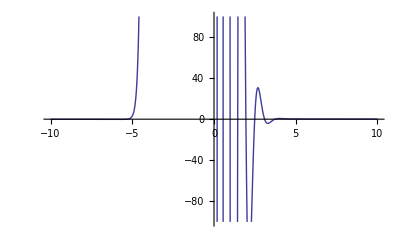

```mathematica
Plot[1/r+ⅇ^(-r^2) (503508.4429664134-5.1465270693010865*^6r+1.80936727944498*^7 r^2-3.0880132252060823*^7 r^3+2.912472497586839*^7 r^4-1.592753695187919*^7 r^5+5.013555851508024*^6 r^6-840308.8140054143 r^7+57927.93823818632 r^8),{r,-10,10}, PlotRange->100]
```

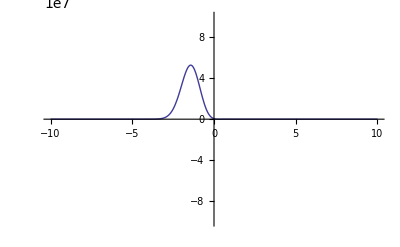

```mathematica
Plot[1/r+ⅇ^(-r^2) (503508.4429664134-5.1465270693010865*^6r+1.80936727944498*^7 r^2-3.0880132252060823*^7 r^3+2.912472497586839*^7 r^4-1.592753695187919*^7 r^5+5.013555851508024*^6 r^6-840308.8140054143 r^7+57927.93823818632 r^8),{r,-10,10}, PlotRange->100000000]
```

Plot of imax=4, n=1:

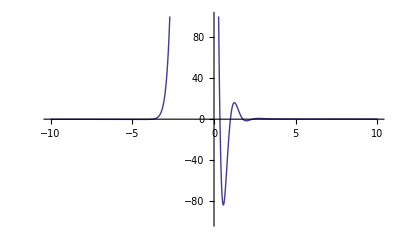

```mathematica
Plot[1/r+ⅇ^(-r^2) (900.0742211629573-4265.998438323818r+5988.955394661216 r^2-3201.245756850285 r^3+573.3645880004416 r^4),{r,-10,10}, PlotRange->100]
```